Compass correction, finding a formula.
Michiel van Wessem

This is an effort to derive a formula from measured compass corrections.

Deviation graph below will be in polar coordinates, with radius indicates the amount of deviation. The value of 1 indicates zero deviation, a value greater than 1 indicating a deviation to the West and a value less than 1 indicates a deviation to the East. 

This is a deviation graph with no deviation at all

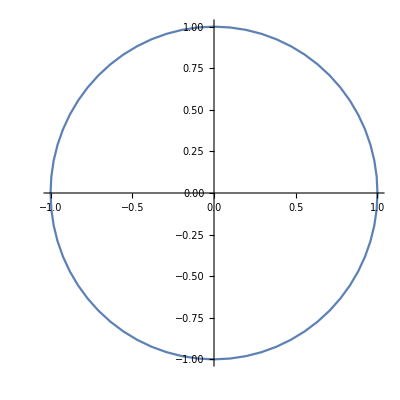

```mathematica
ListPolarPlot[Table[{α,1}, {α,0,2π,π/32}], Joined-> True]
```

Traditionally, compass magnetic coefficients were types A, B, C, D and E.

Here's a description of these types:

Coefficient A effects all headings equally. 

Example:

0.3

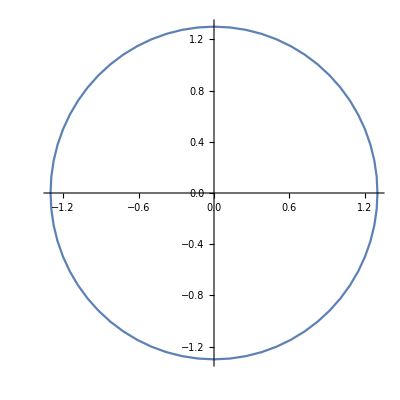

```mathematica
a=.3
ListPolarPlot[Table[{α,1 + a}, {α,0,2π,π/32}], Joined-> True]
```

Coefficient B
Greatest on easterly and westerly headings.

This is a directional offset.

Example:

0.6

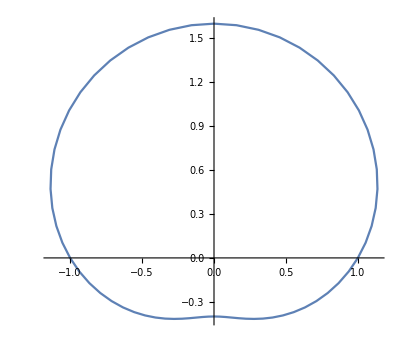

```mathematica
b=.6
ListPolarPlot[Table[{α,1+b*Sin[α]},{α,0,2π,π/32}], Joined-> True]
```

Coefficient C
Similar to B, greatest on northerly and southerly headings, so like B, this is a directional offset.

Example:

0.5

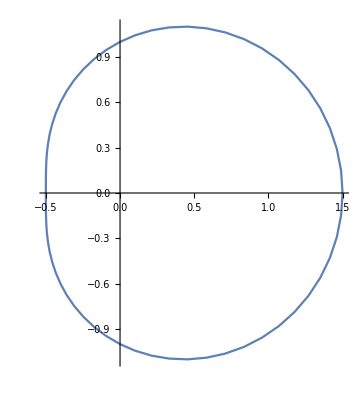

```mathematica
c=.5
ListPolarPlot[Table[{α,1+c* Cos[α]},{α,0,2π,π/32}], Joined-> True]
```

theorem: B and C combined are used to specify a directional bias. This could also be done by with a phase angle and magnitude. 


Coefficient D
Greatest on NW, SW, SE and NE headings

Example:

0.3

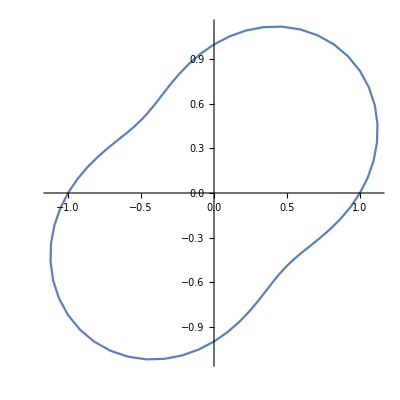

```mathematica
d = .3
ListPolarPlot[Table[{α,1+d*Sin[2α]},{α,0,2π,π/32}],Joined->True]
```

Coefficient E
Greatest on N, S, E, W headings

0.3

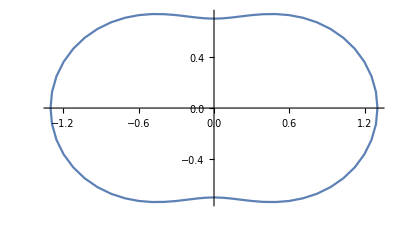

```mathematica
e = .3
ListPolarPlot[Table[{α,1+e*Cos[2α]},{α,0,2π,π/32}],Joined->True]
```

Combined:

0.3

0.4

0.5

0.2

0.3

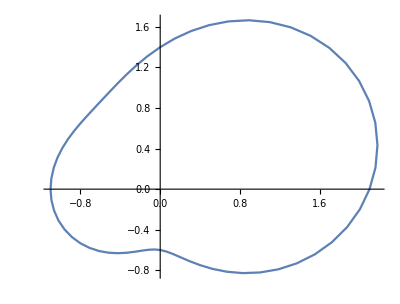

```mathematica
a = .3
b= .4
c = .5
d = .2
e = .3
ListPolarPlot[Table[{α,1+a + b* Sin[α]+c*Cos[α]+ d * Sin[2α]+e*Cos[2α]},{α,0,2π,π/32}],Joined->True]
```

ListPolarPlot[Table[{α,  1 + .5 *Sin[α - .5π] + .4 *Sin[α - .2π ] + .7 Sin[α + π]}, {α,0, 2π,π/100}]]

References:
https://books.google.ca/books?id=ZU2NYPJ08XYC&pg=PA49&lpg=PA49&dq=compass+influence+graph&source=bl&ots=QxgBQ0nV8m&sig=0ROzDq_W0EvkAildXnspkka-AEo&hl=en&sa=X&ved=0ahUKEwjUnK-WiJfMAhVNwmMKHY5ADowQ6AEIJjAB#v=onepage&q=compass%20influence%20graph&f=false